```mathematica
SigmaX={{sigmaX1,c},{c,sigmaX2}}
```

{{sigmaX1,c},{c,sigmaX2}}

```mathematica
SigmaXY={{a},{b}}
```

{{a},{b}}

```mathematica
SigmaY={{sigmaY}}
```

{{sigmaY}}

```mathematica
B=IdentityMatrix[2]-SigmaXY.Inverse[SigmaY].Transpose[SigmaXY].Inverse[SigmaX]
```

{{1+(a b c)/((-c^2+sigmaX1 sigmaX2) sigmaY)-(a^2 sigmaX2)/((-c^2+sigmaX1 sigmaX2) sigmaY),(a^2 c)/((-c^2+sigmaX1 sigmaX2) sigmaY)-(a b sigmaX1)/((-c^2+sigmaX1 sigmaX2) sigmaY)},{(b^2 c)/((-c^2+sigmaX1 sigmaX2) sigmaY)-(a b sigmaX2)/((-c^2+sigmaX1 sigmaX2) sigmaY),1+(a b c)/((-c^2+sigmaX1 sigmaX2) sigmaY)-(b^2 sigmaX1)/((-c^2+sigmaX1 sigmaX2) sigmaY)}}

```mathematica
{vals,vecs}=Eigensystem[B]
```

{{1,(-2 a b c+b^2 sigmaX1+a^2 sigmaX2+c^2 sigmaY-sigmaX1 sigmaX2 sigmaY)/((c^2-sigmaX1 sigmaX2) sigmaY)},{{-(a c-b sigmaX1)/(b c-a sigmaX2),1},{a/b,1}}}

```mathematica
Factor[sigmaX1*sigmaX2*sigmaY^2-b^2*sigmaX1*sigmaY-a^2*sigmaX2*sigmaY+a^2*b^2]
```

(a^2-sigmaX1 sigmaY) (b^2-sigmaX2 sigmaY)

```mathematica
Reduce[2*a*b*c-b^2*sigmaX1-a^2*sigmaX2>(c^2-sigmaX1*sigmaX2)*sigmaY,c,Reals]
```

(sigmaX2<0&&(«1»))||(sigmaX2==0&&((b<0&&(«1»))||(b==0&&sigmaY<0&&(c<0||c>0))||(b>0&&((a<0&&(«1»))||(a==0&&(«1»))||(a>0&&(«1»))))))||(sigmaX2>0&&(«1»))

```mathematica
betacrit[a_,b_,c_,sigmaX1_,sigmaX2_,sigmaY_]:=1/(1-vals[[2]])
```

```mathematica
betacritfunc[a_,b_,c_,sigmaX1_,sigmaX2_,sigmaY_]=Simplify[betacrit[a,b,c,sigmaX1,sigmaX2,sigmaY]]
```

-((c^2-sigmaX1 sigmaX2) sigmaY)/(-2 a b c+b^2 sigmaX1+a^2 sigmaX2)

```mathematica
betacrit2[rx1y_,rx2y_,rx1x2_,sigmaX1_,sigmaX2_,sigmaY_]:=FullSimplify[betacritfunc[rx1y*sigmaX1*sigmaY,rx2y*sigmaX2*sigmaY,rx1x2*sigmaX1*sigmaX2,sigmaX1,sigmaX2,sigmaY]]
```

```mathematica
betacrit2[rx1y,rx2y,rx1x2,sigmaX1,sigmaX2,sigmaY]
```

(1-rx1x2^2 sigmaX1 sigmaX2)/((rx1y^2 sigmaX1+rx2y (rx2y-2 rx1x2 rx1y sigmaX1) sigmaX2) sigmaY)

```mathematica
Plot3D[betacrit2[rx1y,rx2y,0,1,1,1],{rx1y,-0.5,0.5},{rx2y,-0.5,0.5},AxesLabel->{rx1y,rx2y}]
```

-Graphics3D-

```mathematica
ContourPlot[betacritfunc[a,b,0,1,1,1],{a,0.1,1},{b,0.1,1},AxesLabel->Automatic];
```

```mathematica
Animate[Plot[betacritfunc[a,c*a,0,1,1,1],{a,0.1,0.9}],{c,0.1,0.9},AnimationRunning->False];
```

```mathematica
Clear[derivRx1y]
derivRx1y[rx1y_,rx2y_,rx1x2_,sigmaX1_,sigmaX2_,sigmaY_]=FullSimplify[D[betacrit2[rx1y,rx2y,rx1x2,sigmaX1,sigmaX2,sigmaY],rx1y]]
```

(2 sigmaX1 (rx1y-rx1x2 rx2y sigmaX2) (-1+rx1x2^2 sigmaX1 sigmaX2))/((rx1y^2 sigmaX1+rx2y (rx2y-2 rx1x2 rx1y sigmaX1) sigmaX2)^2 sigmaY)

```mathematica
derivRx1y[1,0,0,1,1,1]
```

-2

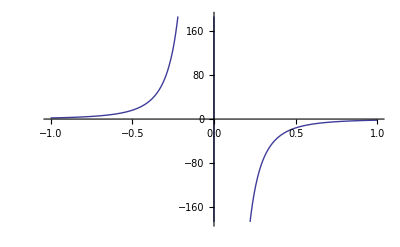

```mathematica
plotRx1y=Plot[derivRx1y[x,0,0,1,1,1],{x,-1,1}]
```